## Load Data

```mathematica
nameScaling=1*10^-8;
SetDirectory[NotebookDirectory[]<>"/ValidationSweeps/"];
folderNames=Select[FileNames[],DirectoryQ];
fileNames=FileNames["ADM*.csv",(NotebookDirectory[]<>"ValidationSweeps/"<>#<>"/")]&/@folderNames;
importedData=ParallelMap[Import[#]&,fileNames,{2}];
labels=importedData[[1,1,1]];
reshappedDatasets=Map[#[[2;;All,2;;(Length[labels]-1)]]&,importedData,{2}];
reshappedLabels=labels[[2;;(Length[labels]-1)]];
```

## Explore Iterations

```mathematica
rhoNumber=5;
Table[
ListLinePlot[
reshappedDatasets[[rhoNumber,i]]//Transpose
,PlotStyle->"LakeColors",PlotRange->5000,Frame->True]
,{i,1,Length[reshappedDatasets[[1]]]}];
```

## Crash Probabilities

```mathematica
rhoCoordinates=N[nameScaling*ToExpression/@folderNames];
probabilitiesVector=N[1-Total[#]/Length[#]]&/@Map[If[Total[Last[#]]>0,1,0]&,reshappedDatasets,{2}];
ListLogLinearPlot[{rhoCoordinates,probabilitiesVector}//Transpose,
PlotRange->{-.1,1.1},
InterpolationOrder->2,
Frame->True,
FrameStyle->Thick,
FrameTicksStyle->15,
Joined->True,
AspectRatio->1,
PlotStyle->Directive[Opacity[.85],Thickness[.0075]]
];
prototypeFunction[x_,k_,c_]:=ⅇ^(-k*x)
nlmMG=NonlinearModelFit[{rhoCoordinates,probabilitiesVector}//Transpose,prototypeFunction[x,k,c],{k,c},x]
p1=LogLinearPlot[
nlm[x]
,{x,.00000001,.0025}];
```

FittedModel[ⅇ^(-22497. x)]

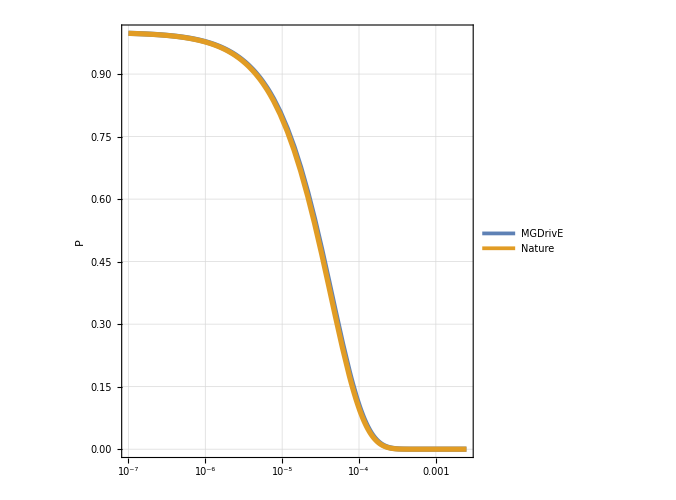
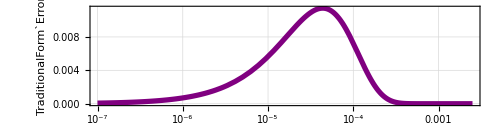

errorMGDrivE.png

```mathematica
logLinear=LogLinearPlot[
{nlmMG[x],popLogFitsNormal[[3]]}
,{x,.0000001,.0025}
,PlotLegends->{"MGDrivE","Nature"}
,Frame->True
,FrameTicksStyle->15
,FrameLabel->{None,"P"}
,BaseStyle->25
,GridLines->Automatic
,FrameStyle->Directive[Gray,Thick]
,GridLinesStyle->Directive[Gray,Thin,Dashed]
,ImageSize->imageSize
,AspectRatio->1
,PlotStyle->Thickness[.0075]
];
legends=(ToString/@(indVectors/namingScalingFactor))[[3]];
logLinearError=LogLinearPlot[(Normal[nlmMG]-popLogFitsNormal[[3]])/1,{x,.0000001,.0025}
,Frame->True
,FrameTicksStyle->11
,BaseStyle->25
,PlotStyle->Directive[Thickness[.0075],Purple]
,GridLines->Automatic
,FrameLabel->{"NHEJ","TraditionalForm`Error"}
,PlotLegends->{"Difference"}
,FrameStyle->Directive[Gray,Thick]
,GridLinesStyle->Directive[Gray,Thin,Dashed]
,ImageSize->imageSize
,AspectRatio->.25
];
Grid[{{logLinear},{logLinearError}}]
Export["errorMGDrivE.png",%,ImageResolution->500]
```